```mathematica
R={#[[1]],#[[3]],#[[4]]}&/@Drop[Import["c:\\eBook2.dat","Table"],1];
```

```mathematica
R=Differences[Log[R]];
```

```mathematica
ListPointPlot3D[R]
```

-Graphics3D-

```mathematica
RandFit={Drop[Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\kurse\eRand1.dat","Table"],1],Drop[Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\kurse\eRand2.dat","Table"],1],Drop[Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\kurse\eRand3.dat","Table"],1]};
```

```mathematica
S=Import["C:\\Book2_Sim\\e.dat","Table"];
```

```mathematica
ListPointPlot3D[S,PlotRange->All]
```

-Graphics3D-

```mathematica
RandS=Table[Sort[Transpose[S][[i]]],{i,3}];RandS=Table[Table[{(i-1)/(Length[RandS[[1]]]-1),RandS[[j,i]]},{i,1,Length[RandS[[1]]]}],{j,3}];
```

```mathematica
RandR=Table[Sort[Transpose[R][[i]]],{i,3}];RandR=Table[Table[{(i-1)/(Length[RandR[[1]]]-1),RandR[[j,i]]},{i,1,Length[RandR[[1]]]}],{j,3}];
```

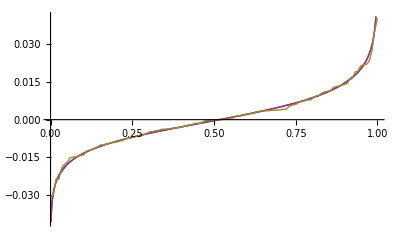

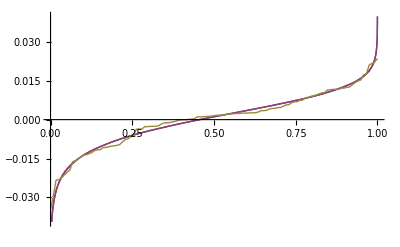

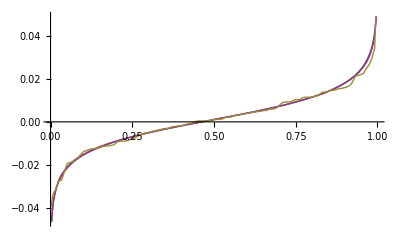

```mathematica
For[i=1,i<=3,i++,Print[ListPlot[{RandFit[[i]],RandS[[i]],RandR[[i]]},Joined->True]]
]
```

```mathematica
Table[Mean[Transpose[S][[i]]],{i,3}]
Table[Mean[Transpose[R][[i]]],{i,3}]
Table[Variance[Transpose[S][[i]]],{i,3}]
Table[Variance[Transpose[R][[i]]],{i,3}]
```

{0.0002364,0.000116811,0.00127513}

{0.000181983,0.0000819829,0.00123612}

{0.00014522,0.000119715,0.000203018}

{0.000141252,0.000118857,0.000217507}

```mathematica
S=Import["c:\\Book2_Sim\\e2.dat","Table"];
```

```mathematica
ListPointPlot3D[S]
```

-Graphics3D-

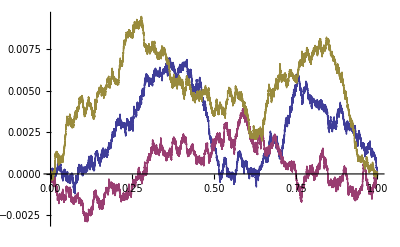

```mathematica
S=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\kurse\simCopula.dat","Table"];RandS=Table[Sort[Transpose[S][[i]]],{i,3}];RandS=Table[Table[{(i-1)/(Length[RandS[[1]]]-1),RandS[[j,i]]-(i-1)/(Length[RandS[[1]]]-1)},{i,1,Length[RandS[[1]]]}],{j,3}];ListPlot[RandS[[1;;3]],Joined->True]
```

```mathematica
Table[Mean[Transpose[RandS[[i]]][[2]]],{i,3}]
```

{0.00195566,0.00123538,0.00103525}

```mathematica
{0.0003055382999999998,0.0014032549333333334,0.0032409049999999997}
```

```mathematica
RandS12={#[[1]],#[[2]]}&/@S;
RandR12={#[[1]],#[[2]]}&/@R;
```

```mathematica
RandS[[1,1;;10]]//N
```

{{0.,0.000423},{0.000333444,0.000714},{0.000666889,0.000749},{0.00100033,0.001073},{0.00133378,0.001445},{0.00166722,0.00172},{0.00200067,0.001816},{0.00233411,0.002068},{0.00266756,0.002902},{0.003001,0.003027}}

```mathematica
wN=Length[RandS12];F={};For[i=1,i≤wN,i++,
AppendTo[F,{RandS12[[i,1]],RandS12[[i,2]],Length[Select[RandS12,#[[1]]<=RandS12[[i,1]]  && #[[2]]<=RandS12[[i,2]]&]]/wN}];
];
```

```mathematica
wN=Length[RandR12];FR={};For[i=1,i≤wN,i++,
AppendTo[FR,{RandR12[[i,1]],RandR12[[i,2]],Length[Select[RandR12,#[[1]]<=RandR12[[i,1]]  && #[[2]]<=RandR12[[i,2]]&]]/wN}];
]
```

```mathematica
Co=Table[{Select[RandR[[1]],#[[2]]==FR[[i,1]]&][[1,1]],Select[RandR[[2]],#[[2]]==FR[[i,2]]&][[1,1]],FR[[i,3]]},{i,wN}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
Show[ListPointPlot3D[Co,PlotStyle->PointSize[Large]],ListPlot3D[F]]
```

-Graphics3D-

```mathematica
RandS12={#[[2]],#[[3]]}&/@S;
RandR12={#[[2]],#[[3]]}&/@R;
```

```mathematica
wN=Length[RandS12];F={};For[i=1,i≤wN,i++,
AppendTo[F,{RandS12[[i,1]],RandS12[[i,2]],Length[Select[RandS12,#[[1]]<=RandS12[[i,1]]  && #[[2]]<=RandS12[[i,2]]&]]/wN}];
];AppendTo[F,{1,0,0}];AppendTo[F,{0,1,0}];AppendTo[F,{0,0,0}];AppendTo[F,{1,1,1}];
```

```mathematica
wN=Length[RandR12];FR={};For[i=1,i≤wN,i++,
AppendTo[FR,{RandR12[[i,1]],RandR12[[i,2]],Length[Select[RandR12,#[[1]]<=RandR12[[i,1]]  && #[[2]]<=RandR12[[i,2]]&]]/wN}];
]
```

```mathematica
Co=Table[{Select[RandR[[2]],#[[2]]==FR[[i,1]]&][[1,1]],Select[RandR[[3]],#[[2]]==FR[[i,2]]&][[1,1]],FR[[i,3]]},{i,wN}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
Show[ListPointPlot3D[Co,PlotStyle->PointSize[Large]],ListPlot3D[F]]
```

-Graphics3D-